### Using compression algorithms to find pockets of reducibility based on traditional fitness functions

```mathematica
NewBCompression2DArrowed[x_List,width_Integer,separatordots_:True]:=Module[{fx=Flatten[x[[1]]],fy=(Flatten[#1/.{Separator->2,Labeled[u_,v_]->u,Dotted[u_,v_,w___]:>With[{z=If[{w}==={},{-1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Dotted[u[[i]]],u[[i]]],{i,Length[u]}]],Arrowed[u_,v_,w___]:>With[{z=If[{w}==={},{1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Arrowed[u[[i]]],u[[i]]],{i,Length[u]}]]}]&)/@Rest[x],ii,jj},GraphicsRow[Insert[Graphics[{ii=0;jj=0;Table[{ii++;If[ii>width,ii=1;jj--];GrayLevel[Switch[If[IntegerQ[#1[[i]]],#1[[i]],#1[[i,1]]],0,0.85,1,0,2,0.5]],Rectangle[{ii-1,jj-1},{ii,jj}],If[separatordots&&#1[[i]]===2,{GrayLevel[0],Disk[{ii-0.5,jj-0.5},.125]},If[Head[#1[[i]]]===Dotted,{Gray,Disk[{ii-0.5,jj-0.5},.35]},If[Head[#1[[i]]]===Arrowed,{GrayLevel[0.5],Polygon[{{ii-0.6,jj-0.2},{ii-0.6,jj-0.8},{ii-0.3,jj-0.5}}]},{}]]],Directive[GrayLevel[0.15],AbsoluteThickness[0.25]],Line[{{ii-1,jj-1},{ii-1,jj},{ii,jj},{ii,jj-1},{ii-1,jj-1}}]},{i,Length[#1]}]},ImageSize->200]&/@Prepend[fy,fx],Graphics[{Arrowheads[Small],Arrow[{{0,0},{1,0}}]},ImageSize->20],2]]]

frequencyData[data_]:=Sort[Function[α,Transpose[{α,(Count[data,#]&/@α)/Length[data]}]][Union[data]],Last[#1]>Last[#2]&]

merge[data_]:=If[Length[data]>1,{{{#1[[1]],#2[[1]]},#1[[2]]+#2[[2]]},##3}&@@Sort[data,#1[[2]]<#2[[2]]&],data]

mergeAll[data_]:=If[Length[data]>1,FixedPoint[merge,data][[1,1]],{data[[1,1]]}]

HuffmanTree[data_,b_]:=mergeAll[frequencyData[Partition[data,b]]]

HassignCode[data_,l_]:=Flatten[MapIndexed[(#1->Mod[#2+1,2])&,data,{-l}]]

HgenerateCode[data_]:=HassignCode[mergeAll[frequencyData[data]],Depth[data[[1]]]]

HuffmanEncode[data_,b_]:=Module[{data1=Partition[data,b],code},code=HgenerateCode[data1];{code,Flatten[data1/.code]}]

HuffmanCodeBlock[data_,s_,lm_]:=Flatten[Module[{f,g,ct=1},(Apply[f,HuffmanTree[data,s],{-2}]/.List->g)//.{g[a_,b_]:>{Arrowed[{0},""],a,b},f[x__]:>{Arrowed[{1},""],Labeled[{x},{x}/.lm]}}]]

DiagramHuffmanEncode[data_,b_]:=Module[{c=First[HuffmanEncode[data,b]],d,fd,lm},lm=MapIndexed[#->First[#2]&,Last/@Reverse[Sort[Reverse/@frequencyData[Partition[data,b]]]]];
{Prepend[Partition[data,b],{}],Join[{HuffmanCodeBlock[data,b,lm]},List/@MapThread[Dotted,{Partition[data,b]/.c,Partition[data,b]/.lm}]]}]
```

```mathematica
NewBCompression2DArrowed[x_List,width_Integer,separatordots_:True]:=Module[{fx=Flatten[x[[1]]],fy=(Flatten[#1/.{Separator->2,Labeled[u_,v_]->u,Dotted[u_,v_,w___]:>With[{z=If[{w}==={},{-1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Dotted[u[[i]]],u[[i]]],{i,Length[u]}]],Arrowed[u_,v_,w___]:>With[{z=If[{w}==={},{1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Arrowed[u[[i]]],u[[i]]],{i,Length[u]}]]}]&)/@Rest[x],ii,jj},GraphicsRow[Insert[Graphics[{ii=0;jj=0;Table[{ii++;If[ii>width,ii=1;jj--];GrayLevel[Switch[If[IntegerQ[#1[[i]]],#1[[i]],#1[[i,1]]],0,0.85,1,0,2,0.5]],Rectangle[{ii-1,jj-1},{ii,jj}],If[separatordots&&#1[[i]]===2,{GrayLevel[0],Disk[{ii-0.5,jj-0.5},.125]},If[Head[#1[[i]]]===Dotted,{Gray,Disk[{ii-0.5,jj-0.5},.35]},If[Head[#1[[i]]]===Arrowed,{GrayLevel[0.5],Polygon[{{ii-0.6,jj-0.2},{ii-0.6,jj-0.8},{ii-0.3,jj-0.5}}]},{}]]],Directive[GrayLevel[0.15],AbsoluteThickness[0.25]],Line[{{ii-1,jj-1},{ii-1,jj},{ii,jj},{ii,jj-1},{ii-1,jj-1}}]},{i,Length[#1]}]},ImageSize->400]&/@Prepend[fy,fx],Graphics[{Arrowheads[Small],Arrow[{{0,0},{1,0}}]},ImageSize->40],2]]]

SetAttributes[Emitted,HoldAll];
Emitted[code_]:=Module[{ans={}},With[{ourEmit=Unique["Emit"]},ourEmit[val_]:=AppendTo[ans,val];
First[Hold[code]/.Emit->ourEmit];Clear[ourEmit]];ans]

LZCMunch[data_]:=Most[Module[{posi={},len=0,loc=0,s},Quiet[While[loc++<Length[data]+1,If[(s=Select[posi+=1,data[[#]]===data[[loc]]&])==={},If[len>0,Emit[{Take[data,{loc-len,loc-1}],P[loc-Last[posi],len]}]];
If[(s=Select[Flatten@Position[data,data[[loc]],{1}],#<loc&])==={},(*new element*)Emit[{{data[[loc]]}}];len=0,posi=s;
len=1],len+=1;posi=s]],Part::partw]//Emitted]]

BreakList[list_,pts_]:=Take[list,#+{0,-1}]&/@Partition[FoldList[Plus,1,pts],2,1]

FibonacciDigits[n_]:=Take@@RealDigits[N[#,N[Log10[#]+3]]&[n √5/GoldenRatio^2+1/2],GoldenRatio]

FibonacciCode[n_]:=Rest[RotateLeft[Join[FibonacciDigits[n],{0,1}]]]

FLZCEncodePieceX[bits_List]:={Arrowed[{0},""],Dotted[FibonacciCode[Length[bits]],Length[bits]],Labeled[bits,""]}

FLZCEncodePieceX[x:P[offset_,len_]]:={Arrowed[{1},""],Dotted[FibonacciCode[len],len],Labeled[FibonacciCode[offset],StringForm["⊲``⊲",offset]]}

FLZCEncodePiece[bits_List]:=Join[{0},FibonacciCode[Length[bits]],bits]

FLZCEncode[data_]:=If[Sort[#]===#&[FLZCEncodePiece/@#],First[#],Last[#]]&/@LZCMunch[data]

DiagramFLZCEncode[data_]:=Module[{c=Split[Flatten[FLZCEncode[data]],Head[#1]===Head[#2]&]/.{a__P}:>a},{BreakList[data,llen/@c],FLZCEncodePieceX/@c}]
```

#### At each line

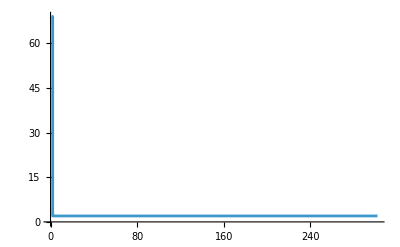
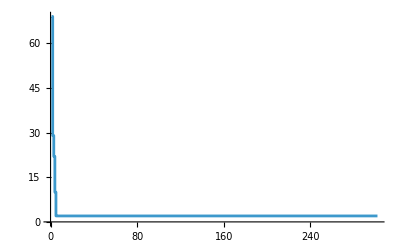
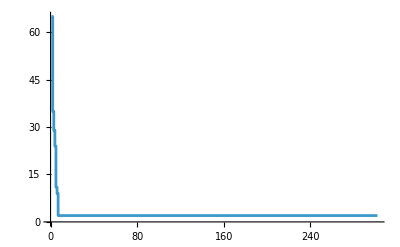
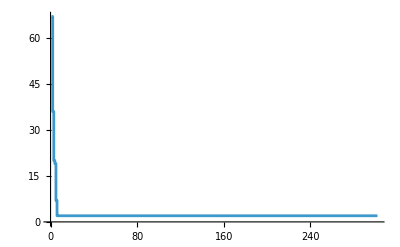
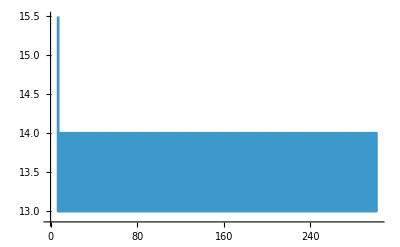
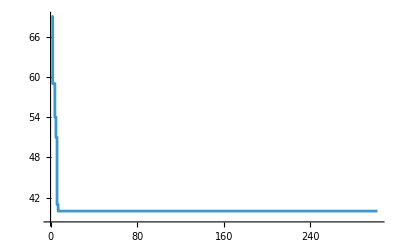
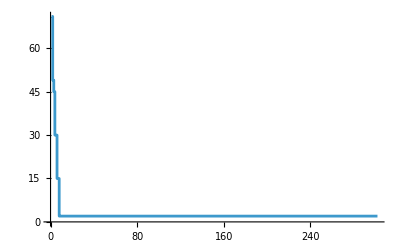
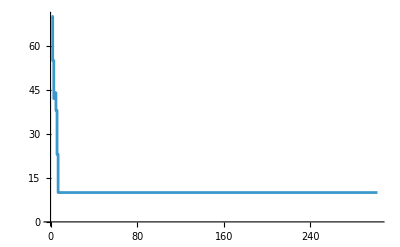
{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-2,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-4,-Graphics-4,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-8,-Graphics-8,-Graphics-9,-Graphics-9,-Graphics-9,-Graphics-10,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-14,-Graphics-14,-Graphics-14,-Graphics-14,-Graphics-15,-Graphics-16,-Graphics-17,-Graphics-17,-Graphics-17,-Graphics-18,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-20,-Graphics-21,-Graphics-22,-Graphics-23,-Graphics-23,-Graphics-25,-Graphics-25,-Graphics-28,-Graphics-28,-Graphics-39,-Graphics-45,-Graphics-64}

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-2,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-4,-Graphics-4,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-8,-Graphics-8,-Graphics-9,-Graphics-9,-Graphics-9,-Graphics-10,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-14,-Graphics-14,-Graphics-14,-Graphics-14,-Graphics-15,-Graphics-16,-Graphics-17,-Graphics-17,-Graphics-17,-Graphics-18,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-20,-Graphics-21,-Graphics-22,-Graphics-23,-Graphics-23,-Graphics-25,-Graphics-25,-Graphics-28,-Graphics-28,-Graphics-39,-Graphics-45,-Graphics-64}

```mathematica
ParallelMap[Labeled[ListStepPlot[Length[FLZCEncode[#]]&/@CellularAutomaton[{#[[1, 1]],2,2},RandomInteger[1,500],300]],#[[2]]]&,Normal[{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]]]
```

```mathematica
compressedrowlengths = [[All, 1, 1, 1, 2,1, 1, 3, 1, 3, 1]]
```

```mathematica
Iconize[compressedrowlengths]
```

```mathematica
frequencyData[data_]:=Sort[Function[α,Transpose[{α,(Count[data,#]&/@α)/Length[data]}]][Union[data]],Last[#1]>Last[#2]&]

merge[data_]:=If[Length[data]>1,{{{#1[[1]],#2[[1]]},#1[[2]]+#2[[2]]},##3}&@@Sort[data,#1[[2]]<#2[[2]]&],data]

mergeAll[data_]:=If[Length[data]>1,FixedPoint[merge,data][[1,1]],{data[[1,1]]}]

HuffmanTree[data_,b_]:=mergeAll[frequencyData[Partition[data,b]]]

HassignCode[data_,l_]:=Flatten[MapIndexed[(#1->Mod[#2+1,2])&,data,{-l}]]

HgenerateCode[data_]:=HassignCode[mergeAll[frequencyData[data]],Depth[data[[1]]]]

HuffmanEncode[data_,b_]:=Module[{data1=Partition[data,b],code},code=HgenerateCode[data1];{code,Flatten[data1/.code]}]

HuffmanCodeBlock[data_,s_,lm_]:=Flatten[Module[{f,g,ct=1},(Apply[f,HuffmanTree[data,s],{-2}]/.List->g)//.{g[a_,b_]:>{Arrowed[{0},""],a,b},f[x__]:>{Arrowed[{1},""],Labelled[{x},{x}/.lm]}}]]

DiagramHuffmanEncode[data_,b_]:=Module[{c=First[HuffmanEncode[data,b]],d,fd,lm},lm=MapIndexed[#->First[#2]&,Last/@Reverse[Sort[Reverse/@frequencyData[Partition[data,b]]]]];
{Prepend[Partition[data,b],{}],Join[{HuffmanCodeBlock[data,b,lm]},List/@MapThread[Dotted,{Partition[data,b]/.c,Partition[data,b]/.lm}]]}]

ArrowedCompressionGraphic[f_,data_]:=With[{fdata=f[data]},GraphicsRow[{ArrayPlot[data,ImageSize->150],Graphics[{Arrowheads[Small],Arrow[{{0,0},{1,0}}]},ImageSize->20],ArrayPlot[Partition[PadRight[fdata,Ceiling[Length[fdata]/Length[First[data]]]*Length[First[data]]],Length[First[data]]],ImageSize->150]}]]

R30Center[n_]:=Module[{a=1},Table[First[IntegerDigits[a,a=BitXor[a,BitOr[2a,4a]];2,i]],{i,n}]]

cdatax=Join[(CellularAutomaton[#1,CenterArray[{1},129],63]&)/@{254,90,30},((Take[#1,{66,-66}]&)/@Drop[CellularAutomaton[#1,CenterArray[{1},259],127],64]&)/@{30},{Take[#,{37,-37}]&/@Take[CellularAutomaton[{478,{2,{{0,2,0},{2,1,2},{0,2,0}}},{1,1}},CenterArray[{{1}},{201,201}],{{{100}}}],{70,-69}],Partition[R30Center[8256],129]}];

GraphicsGrid[Partition[MapIndexed[Labeled[Function[x,ArrowedCompressionGraphic[(Flatten[First/@Flatten[Last[DiagramHuffmanEncode[Flatten[Partition[#,{2,3}]],6]]]])&,x]][#1],Text[Style["("<>FromLetterNumber[First[#2]]<>")",Italic]],Left]&,cdatax],2],ImageSize->700]
```

#### Total complexity with masked rules

```mathematica
randmaskrus = Module[{rubits, maskbits, rurandmask, newru},
Keys[KeyMap[Function[key, 
rubits = IntegerDigits[key[[1]], 2, 32];
maskbits = IntegerDigits[key[[2]], 2, 32];
rurandmask = MapAt[RandomChoice[{0, 1}]&, rubits, Position[maskbits, 0]];newru = FromDigits[rurandmask, 2]], {{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]]]
];
```

```mathematica
compressedevocas = ParallelMap[HuffmanEncode[Flatten[CellularAutomaton[{#1,2,2},RandomInteger[1,500],300]], 2]&, randmaskrus];
```

```mathematica
MapThread[Labeled[ArrayPlot[Partition[#1, 500]], #2]&, {compressedevocas[[All ,-1]], Values[{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]]}]
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-2,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-4,-Graphics-4,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-8,-Graphics-8,-Graphics-9,-Graphics-9,-Graphics-9,-Graphics-10,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-14,-Graphics-14,-Graphics-14,-Graphics-14,-Graphics-15,-Graphics-16,-Graphics-17,-Graphics-17,-Graphics-17,-Graphics-18,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-20,-Graphics-21,-Graphics-22,-Graphics-23,-Graphics-23,-Graphics-25,-Graphics-25,-Graphics-28,-Graphics-28,-Graphics-39,-Graphics-45,-Graphics-64}

```mathematica
KeyValueMap[Labeled[ArrayPlot[CellularAutomaton[{#1,2,2},RandomInteger[1,500],300]],#2]&,KeyMap[Function[key, 
rubits = IntegerDigits[key[[1]], 2, 32];
maskbits = IntegerDigits[key[[2]], 2, 32];
rurandmask = MapAt[RandomChoice[{0, 1}]&, rubits, Position[maskbits, 0]];newru = FromDigits[rurandmask, 2]], {{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]]]
```

### Addressing problem of masked rules

```mathematica
{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]
```

<|{0,65815}→0,{276,285295007}→1,{1048868,156317055}→2,{1049892,3507586495}→2,{139469092,424769023}→3,{139473252,3646010879}→3,{269484468,424769023}→3,{1343260068,3646010879}→3,{3222308132,3507602879}→3,{1343260084,3646027263}→4,{3360731492,3646027263}→4,{269616548,4120108543}→5,{269632932,4154449919}→5,{613570916,4258528767}→5,{2416985508,4189312511}→5,{2551203236,4260494847}→5,{35541860,2145386495}→6,{204478820,1039367679}→6,{269501860,4122205695}→6,{303974308,4292870143}→6,{749754724,4260494847}→6,{2419066276,4122074623}→6,{2419082660,4156415999}→6,{70261092,494108159}→7,{749738340,2113011199}→7,{815792532,968316927}→7,{947913108,1033330687}→7,{1476690836,4187478015}→7,{2419066292,4122074623}→7,{2453424036,4294836223}→7,{2961310100,4120371199}→7,{1889699220,4260888575}→8,{2555536804,4294967295}→8,{336612772,4260625919}→9,{2555405732,4260625919}→9,{3970996580,4260494847}→9,{716968804,4294967295}→10,{335546772,1035427839}→11,{336727476,4294967295}→11,{2484211124,4294967295}→11,{370806196,4294967295}→12,{1823512932,4294967295}→12,{2485258644,4294967295}→12,{2489461140,4294967295}→12,{2518289844,4294967295}→12,{303695284,4290502143}→13,{2451178932,4290502143}→13,{2519337364,4294967295}→13,{2623678868,4294967295}→13,{3938227044,4294967295}→13,{503843220,1069506559}→14,{848954804,4160749567}→14,{1445759892,4290764799}→14,{3164735892,4260888575}→14,{1344570260,4290764799}→15,{2418147732,4160749567}→16,{649615716,4294704639}→17,{849086372,4294967295}→17,{2452226452,4160749567}→17,{3028421012,4294967295}→18,{814745012,4294967295}→19,{880937364,4156547071}→19,{2486177204,4290764799}→19,{2487363988,4160749567}→19,{2585396644,4294967295}→19,{848823732,4294967295}→20,{2619476372,4294967295}→21,{1514709396,4294967295}→22,{438044596,4288667647}→23,{3662193044,4294967295}→23,{615536996,2147483647}→25,{3029470644,4294967295}→25,{2417100196,4294967295}→28,{3392835940,4294967295}→28,{3063549364,4294967295}→39,{2417362868,4294967295}→45,{2455381412,4294967295}→64|>

```mathematica
RuleSequencePlot[{n_, k_, r_}, ops:OptionsPattern[{ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= 
ArrayPlot[{IntegerDigits[n, k, k^(2r+1)]},ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize], ops]
```

```mathematica
MapAt[]
```

```mathematica
KeyMap[Function[key, 
rubits = IntegerDigits[key[[1]], 2, 32];
maskbits = IntegerDigits[key[[2]], 2, 32];
rurandmask = MapAt[RandomChoice[{0, 1}]&, rubits, Position[maskbits, 0]];newru = FromDigits[rurandmask, 2]], {{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]];
```

```mathematica
KeyMap[RuleSequencePlot[{#, 2, 2}]&, ]
```

<|-Graphics-→0,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→5,-Graphics-→5,-Graphics-→5,-Graphics-→6,-Graphics-→6,-Graphics-→6,-Graphics-→6,-Graphics-→6,-Graphics-→6,-Graphics-→6,-Graphics-→7,-Graphics-→7,-Graphics-→7,-Graphics-→7,-Graphics-→7,-Graphics-→7,-Graphics-→7,-Graphics-→7,-Graphics-→8,-Graphics-→8,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→10,-Graphics-→11,-Graphics-→11,-Graphics-→11,-Graphics-→12,-Graphics-→12,-Graphics-→12,-Graphics-→12,-Graphics-→12,-Graphics-→13,-Graphics-→13,-Graphics-→13,-Graphics-→13,-Graphics-→13,-Graphics-→14,-Graphics-→14,-Graphics-→14,-Graphics-→14,-Graphics-→15,-Graphics-→16,-Graphics-→17,-Graphics-→17,-Graphics-→17,-Graphics-→18,-Graphics-→19,-Graphics-→19,-Graphics-→19,-Graphics-→19,-Graphics-→19,-Graphics-→20,-Graphics-→21,-Graphics-→22,-Graphics-→23,-Graphics-→23,-Graphics-→25,-Graphics-→25,-Graphics-→28,-Graphics-→28,-Graphics-→39,-Graphics-→45,-Graphics-→64|>

```mathematica
KeyValueMap[Labeled[ArrayPlot[CellularAutomaton[{#1,2,2},RandomInteger[1,500],300]],#2]&,KeyMap[Function[key, 
rubits = IntegerDigits[key[[1]], 2, 32];
maskbits = IntegerDigits[key[[2]], 2, 32];
rurandmask = MapAt[RandomChoice[{0, 1}]&, rubits, Position[maskbits, 0]];newru = FromDigits[rurandmask, 2]], {{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]]]
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-2,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-4,-Graphics-4,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-5,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-6,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-8,-Graphics-8,-Graphics-9,-Graphics-9,-Graphics-9,-Graphics-10,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-14,-Graphics-14,-Graphics-14,-Graphics-14,-Graphics-15,-Graphics-16,-Graphics-17,-Graphics-17,-Graphics-17,-Graphics-18,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-20,-Graphics-21,-Graphics-22,-Graphics-23,-Graphics-23,-Graphics-25,-Graphics-25,-Graphics-28,-Graphics-28,-Graphics-39,-Graphics-45,-Graphics-64}

### Using image processing

### Density flow of class-4 from NKS

```mathematica
2*1150
```

2300

```mathematica
CellularAutomaton[{1635,{3,1}},{{1},0},{3000,{-1150,1150}}]
```

```mathematica
ListLinePlot[Count[#, 1]/Length[#]&/@CellularAutomaton[{1635,{3,1}},{{1},0},{20000,{-1150,1150}}],ImageSize->Large]
```

-Graphics-

```mathematica
ListLinePlot[Count[#, 1]/Length[#]&/@CellularAutomaton[{1635,{3,1}},RandomInteger[2, 200],10000],ImageSize->Large]
```

-Graphics-

```mathematica
ListLinePlot[Count[#, 1]/Length[#]&/@CellularAutomaton[{1635,{3,1}},RandomInteger[2, 200],10000],ImageSize->Large]
```

-Graphics-

#### Rule 30 for comp

```mathematica
ListLinePlot[Count[#, 1]/Length[#]&/@CellularAutomaton[30,{{1},0},{10000,{-1150,1150}}],ImageSize->Large]
```

-Graphics-